```mathematica
Clear[Δa,Δb,α,β1,β2,β3,β4,β5,βA,βB,fAGL, fBGL,DifffAB];
fBGL=-(3 α^2)/(4 (3 β1+3 β2+β3+β4+β5));
fAGL=-α^2/(4 (β2+β4+β5));
DifffAB=FullSimplify[fAGL-fBGL,Assumptions->{{α,β1,β2,β3,β4,β5}∈Reals}]
```

1/4 α^2 (-1/(β2+β4+β5)+3/(3 β1+3 β2+β3+β4+β5))

0.0000861733

0.002463

7.88565×10^10 (2-0.8688 t)

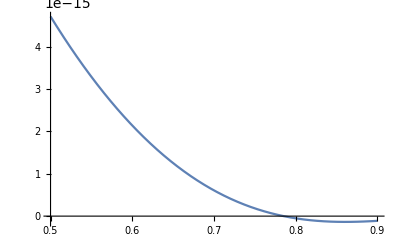

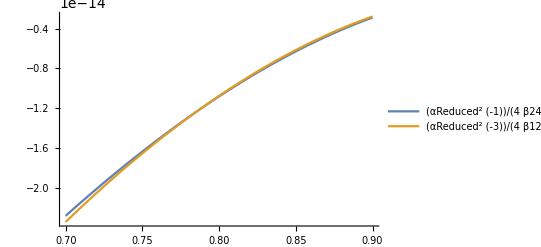

```mathematica
Clear[t,Δa,Δb,α,β1,β2,β3,β4,β5,βA,βB,β245Reduced,β12345Reduced,c1,c2,c3,c4,c5,fAGL, fBGL,DifffAB];
(**pressure is 32 bar**)
c1=-0.0402;c2 = -0.1583;c3=-0.0267;c4=-0.3388;c5=-0.3717;
c245=c2+c4+c5;
c12=c1+c2;
c345=c3+c4+c5;
kb=8.617333262145 10^-5(**eV.K^-1*)
Tc=2.463 10^-3(*mK, kevin*)
(*********)
αReduced=1/3 (t-1);
β245Reduced=(1/(30 π^2 kb^2 Tc^2) (7/8 Zeta[3])) (2+t c245)
β12345Reduced=(1/(30 π^2 kb^2 Tc^2) (7/8 Zeta[3])) (3 (1+t c12)+(2+t c345));
Plot[1/4 αReduced^2 (-1/β245Reduced+3/β12345Reduced),{t,0.5,0.9}]
Plot[{1/4 αReduced^2 (-1/β245Reduced),1/4 αReduced^2 (-3/β12345Reduced)},{t,0.7,0.9},PlotLegends->"Expressions"]
```